```mathematica
"Вычисляем n+1 значение"
n =7
  a=0;  b =8; h = (b-a)/n
"Таблица данной функции"
XData = {}; YouData = {};
For[i=0,i≤n, i++,
x1data[i]=a+i*h;
you1data[i]=N[Power[x1data[i],1/3]];
XData=Append[XData, x1data[i]];
YouData = Append[YouData, you1data[i]];];
Array[x1data,{n+1,0}];
Array[you1data, {n+1,0}];
MatrixForm[XData]
MatrixForm[YouData]
```

Вычисляем n+1 значение

7

8/7

Таблица данной функции

(0
8/7
16/7
24/7
32/7
40/7
48/7
8)

(0.
1.04552
1.31727
1.50789
1.65965
1.78781
1.89983
2.)

```mathematica
({{0.}, {1.2599210498948732}, {1.5874010519681994}, {1.8171205928321397}, {2.}})

"Вычисляем таблицу разностей"
```

```mathematica
Array[diff, {n+1, n+1},{0,0}];
"Заполняются элементы пустых клеток таблицы"
For[j=1,j≤n,j++,
For[i=n, i≥n-j,i--,diff[i,j]=""]];
"Заполняются элементы с разностью"
For[i=0,i≤n,i++,diff[i,0]=you1data[i]];
For[j=1,j≤n,j++,
For[i=0,i≤n-j,i++,
diff[i,j]=(diff[i+1,j-1]-diff[i,j-1])/(x1data[i+j]-x1data[i])]];
tabl1=Array[diff,{n+1,n+1},{0,0}];
PaddedForm[TableForm[tabl1],{6,5}]
"Вычисляем таблицу разностей"
```

Заполняются элементы пустых клеток таблицы

Заполняются элементы с разностью

0.00000 |  0.91483 | -0.29621 |  0.07734 | -0.01589 |  0.00266 | -0.00038 |  0.00005
 1.04552 |  0.23778 | -0.03106 |  0.00472 | -0.00066 |  0.00008 | -9.09572×10^-6 | 
 1.31727 |  0.16680 | -0.01488 |  0.00170 | -0.00019 |  0.00002 |  | 
 1.50789 |  0.13279 | -0.00904 |  0.00083 | -0.00008 |  |  | 
 1.65965 |  0.11213 | -0.00618 |  0.00048 |  |  |  | 
 1.78781 |  0.09802 | -0.00454 |  |  |  |  | 
 1.89983 |  0.08765 |  |  |  |  |  | 
 2.00000 |  |  |  |  |  |  |

Вычисляем таблицу разностей

```mathematica
"Интреполяционные многочлены 1, 2, 3, 4, 5 порядка"
```

```mathematica
plan = diff[0,0]+diff[0,1]*(x-x1data[0]);
n =7; list = List[plan];
For[i=2,i≤n,i++,
plan=list[[i-1]]+diff[0,i]*Product[(x-x1data[i]),{i,0,i-1}];
list=Append[list,plan]];
nwtn[x_]:=N[list[[n]]];
Column[list]
```

0.+0.914826 x
0.+0.914826 x-0.296207 (-8/7+x) x
0.+0.914826 x-0.296207 (-8/7+x) x+0.0773358 (-16/7+x) (-8/7+x) x
0.+0.914826 x-0.296207 (-8/7+x) x+0.0773358 (-16/7+x) (-8/7+x) x-0.0158852 (-24/7+x) (-16/7+x) (-8/7+x) x
0.+0.914826 x-0.296207 (-8/7+x) x+0.0773358 (-16/7+x) (-8/7+x) x-0.0158852 (-24/7+x) (-16/7+x) (-8/7+x) x+0.00266454 (-32/7+x) (-24/7+x) (-16/7+x) (-8/7+x) x
0.+0.914826 x-0.296207 (-8/7+x) x+0.0773358 (-16/7+x) (-8/7+x) x-0.0158852 (-24/7+x) (-16/7+x) (-8/7+x) x+0.00266454 (-32/7+x) (-24/7+x) (-16/7+x) (-8/7+x) x-0.000376613 (-40/7+x) (-32/7+x) (-24/7+x) (-16/7+x) (-8/7+x) x
0.+0.914826 x-0.296207 (-8/7+x) x+0.0773358 (-16/7+x) (-8/7+x) x-0.0158852 (-24/7+x) (-16/7+x) (-8/7+x) x+0.00266454 (-32/7+x) (-24/7+x) (-16/7+x) (-8/7+x) x-0.000376613 (-40/7+x) (-32/7+x) (-24/7+x) (-16/7+x) (-8/7+x) x+0.0000459397 (-48/7+x) (-40/7+x) (-32/7+x) (-24/7+x) (-16/7+x) (-8/7+x) x

```mathematica
Column[Collect[list,x]]
```

0.+0.914826 x
0.+1.25335 x-0.296207 x^2
0.+1.45537 x-0.561358 x^2+0.0773358 x^3
0.+1.59764 x-0.789586 x^2+0.186263 x^3-0.0158852 x^4
0.+1.70673 x-0.988455 x^2+0.30807 x^3-0.0463371 x^4+0.00266454 x^5
0.+1.79485 x-1.1645 x^2+0.434559 x^3-0.0881488 x^4+0.00912076 x^5-0.000376613 x^6
0.+1.86855 x-1.32249 x^2+0.561834 x^3-0.138551 x^4+0.0196213 x^5-0.00147917 x^6+0.0000459397 x^7

```mathematica
"Вычисление интерполяционного многочлена с помощью встроенной фукнции"
```

```mathematica
data = {{0,0},{8/7,1.0455159171494202},{16/7,1.31727},{24/7, 1.50789},{32/7, 1.65965},{40/7, 1.78781},{48/7, 1.89983},{8,2.}}
inpln:=InterpolatingPolynomial[data,x];
Collect[inpln,x]
```

{{0,0},{8/7,1.04552},{16/7,1.31727},{24/7,1.50789},{32/7,1.65965},{40/7,1.78781},{48/7,1.89983},{8,2.}}

0.+1.86851 x-1.32242 x^2+0.561787 x^3-0.138537 x^4+0.0196191 x^5-0.001479 x^6+0.0000459346 x^7

```mathematica
{{0,0},{8/5,1.259922},{4,1.587388},{6,1.817103},{8,1.999987}}
```

0.+1.10017 x-0.310704 x^2+0.041883 x^3-0.00204111 x^4

```mathematica
Plot[{Power[x,1/3],nwtn[x],Abs[Power[x,1/3]-nwtn[x]]},{x,-2,10}, PlotLabels->"Expressions"]
```

-Graphics-

```mathematica
Plot[{Power[x,1/3],nwtn[x]},{x,-4,12}, PlotLabels->"Expressions"]
```

-Graphics-

```mathematica
Pln={};P[n+1] = 0;

For[i=n,i≥0,i--,P[i]=diff[0,i]+(x-x1data[i])*P[i+1];
Pln=Append[Pln,P[i]];]
ColumnForm[Pln]
```

0.0000459397
-0.000376613+0.0000459397 (-48/7+x)
0.00266454+(-0.000376613+0.0000459397 (-48/7+x)) (-40/7+x)
-0.0158852+(0.00266454+(-0.000376613+0.0000459397 (-48/7+x)) (-40/7+x)) (-32/7+x)
0.0773358+(-0.0158852+(0.00266454+(-0.000376613+0.0000459397 (-48/7+x)) (-40/7+x)) (-32/7+x)) (-24/7+x)
-0.296207+(0.0773358+(-0.0158852+(0.00266454+(-0.000376613+0.0000459397 (-48/7+x)) (-40/7+x)) (-32/7+x)) (-24/7+x)) (-16/7+x)
0.914826+(-0.296207+(0.0773358+(-0.0158852+(0.00266454+(-0.000376613+0.0000459397 (-48/7+x)) (-40/7+x)) (-32/7+x)) (-24/7+x)) (-16/7+x)) (-8/7+x)
0.+(0.914826+(-0.296207+(0.0773358+(-0.0158852+(0.00266454+(-0.000376613+0.0000459397 (-48/7+x)) (-40/7+x)) (-32/7+x)) (-24/7+x)) (-16/7+x)) (-8/7+x)) x

```mathematica
P[0]
nwtn[x_]:=P[0];m=40
XDAT={};YDAT={};nwtnDAT={};MR={};
For [i=0,i<=m,i++ ,
xdatas[i]=a+i*(h/10);
ydatas[i]=N[Power[xdatas[i],1/3]];
x=xdatas[i];
nwtndatas[i]=nwtn[x];
mr[i]=Abs[ydatas[i]-nwtndatas[i]];
XDAT=Append[XDAT,xdatas[i]];
YDAT=Append[YDAT,ydatas[i]];
nwtnDAT=Append[nwtnDAT,nwtndatas[i]];
MR=Append[MR,mr[i]];];
MatrixForm[N[XDAT]] MatrixForm[YDAT] MatrixForm[nwtnDAT] MatrixForm[MR]
```

0.+(0.629961+(-0.116555+(0.0173892+(-0.00204104+0.000554232 (-32/5+x)) (-24/5+x)) (-16/5+x)) (-8/5+x)) x

40

(0.
0.1577
0.298436
0.424089
0.53638
0.636883
0.727026
0.808101
0.881271
0.947575
1.00794
1.06317
1.11399
1.16101
1.20477
1.24571
1.28421
1.32058
1.35506
1.38786
1.41911
1.44894
1.47741
1.50459
1.5305
1.55517
1.57863
1.60089
1.62198
1.64195
1.66088
1.67887
1.69606
1.71263
1.72882
1.74494
1.76133
1.77843
1.79675
1.8169
1.83957) (0.
0.16
0.32
0.48
0.64
0.8
0.96
1.12
1.28
1.44
1.6
1.76
1.92
2.08
2.24
2.4
2.56
2.72
2.88
3.04
3.2
3.36
3.52
3.68
3.84
4.
4.16
4.32
4.48
4.64
4.8
4.96
5.12
5.28
5.44
5.6
5.76
5.92
6.08
6.24
6.4) (0.
0.385183
0.385554
0.358885
0.325394
0.291435
0.259459
0.230397
0.204496
0.181668
0.16167
0.144191
0.128902
0.115486
0.103655
0.0931529
0.0837678
0.0753263
0.0676944
0.0607744
0.0545012
0.0488378
0.04377
0.0393013
0.0354466
0.0322267
0.0296618
0.0277656
0.0265381
0.0259599
0.0259852
0.026535
0.0274909
0.0286878
0.0299076
0.030872
0.031236
0.0305809
0.0284074
0.0241288
0.0170642) (0.
0.542884
0.68399
0.782974
0.861774
0.928318
0.986485
1.0385
1.08577
1.12924
1.16961
1.20736
1.24289
1.2765
1.30843
1.33887
1.36798
1.39591
1.42276
1.44863
1.47361
1.49777
1.52118
1.54389
1.56595
1.5874
1.60829
1.62865
1.64851
1.66791
1.68687
1.7054
1.72355
1.74132
1.75873
1.77581
1.79256
1.80901
1.82516
1.84103
1.85664)

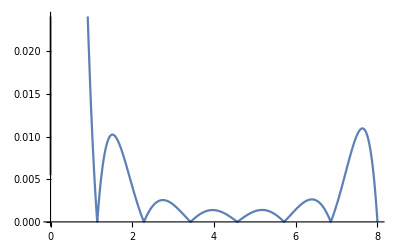

```mathematica
Plot[Abs[Power[x,1/3]-nwtn[x]],{x,0,8}]
```

```mathematica
FindMaximum[{Abs[x^(1/3)-nwtn[x]], 0 < x < 8},x]
```

{0.290296,{x→0.0916424}}

```mathematica
{1.9999999157496762,{x->7.999998988996157}}
```

```mathematica
f[x_]:=Product[x-x1data[k],{k,0,n}]
Collect[f[x],x]
```

(8-{0,2,4,6,8}[1]) (8-{0,2,4,6,8}[2]) (8-{0,2,4,6,8}[3]) (8-{0,2,4,6,8}[4])

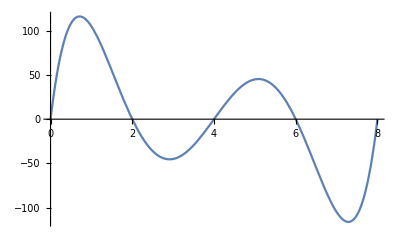

```mathematica
Plot[x^5-20*x^4+140*x^3-400*x^2+384*x,{x,0,8}]
```

```mathematica
FindMaximum[{f[x], 0 <= x <= 8},{x,0}]
```

FindMaximum::nrnum: The function value -(0.-{0,2,4,6,8}[1]) (0.-{0,2,4,6,8}[2]) (0.-{0,2,4,6,8}[3]) (0.-{0,2,4,6,8}[4]) is not a real number at {x} = {0.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

FindMaximum::nrnum: The function value -(-6.05545×10^-6-{0,2,4,6,8}[1]) (-6.05545×10^-6-{0,2,4,6,8}[2]) (-6.05545×10^-6-{0,2,4,6,8}[3]) (-6.05545×10^-6-{0,2,4,6,8}[4]) is not a real number at {x} = {-6.05545×10^-6}.

FindMaximum::nrnum: The function value -(0.000993945-{0,2,4,6,8}[1]) (0.000993945-{0,2,4,6,8}[2]) (0.000993945-{0,2,4,6,8}[3]) (0.000993945-{0,2,4,6,8}[4]) is not a real number at {x} = {0.000993945}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[-((x-{0,2,4,6,8}[1]) (x-{0,2,4,6,8}[2]) (x-{0,2,4,6,8}[3]) (x-{0,2,4,6,8}[4]))],Block},{0,{{{},1,0,Hold[x],0,0}}},{{«1»}},«1»,{904,MachinePrecision,{{Automatic},{Hold[-((x+Times[«2»]) (x+Times[«2»]) (x+Times[«2»]) (x+Times[«2»]))],Block}},True,{{Automatic,«3»,RuntimeErrorHandler→($Failed&)},{},«9»,WVM},FindMaximum,Automatic,None},{None,None,None}] failed at {0.001}.

FindMaximum[{f[x],0≤x≤8},{x,0}]

```mathematica
{116.20583,{x->0.7111342}}
```

```mathematica
{116.20583067036293,{x->0.7111342650817073}}
```

{116.206,{8→0.711134}}